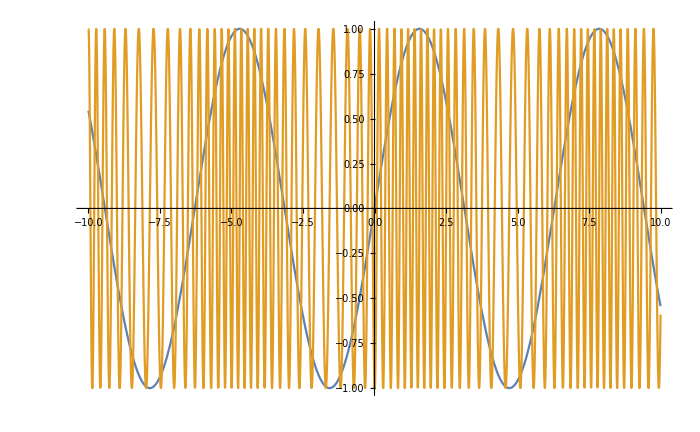

```mathematica
f1[x_]:=Sin[x];
c1[x_]:=Sin[10*x];
Plot[{f1[x],Sin[20*x+(-Cos[x]*8)]},{x,-10,10},ImageSize->700]
(*p:=Range[-10,10,.01]
ListLinePlot[{f1[p],c1[(f1[p]+1)/2*p]},ImageSize->800]*)
```

```mathematica
f1[x_]:=2Sin[x]
f2[x_]:=Cos[2x]
s1[x_]:=Sin[.5x]
```

```mathematica
ff[x_]:=If[Abs[s1[x]]>0.5,f1[x],f2[x]]
```

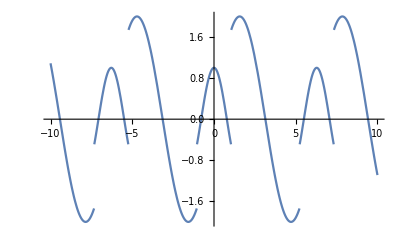

```mathematica
Plot[{ff[x]},{x,-10,10}]
```